```mathematica
Nequil = {};
LoadR ={};
For[i = -3,i≤5,i++,
R = 10^i;
z = DSolve[y'[t] == R - 0.2*y[t] - 1000*y[t]*(y[t]-1), y[t],t]//Simplify;
Natom = Limit[y[t],t->Infinity]/.z;
AppendTo[Nequil, Natom[[1]]];
AppendTo[LoadR,R]]
```

```mathematica
data=Thread[{LoadR,Nequil}];
```

```mathematica
data
```

{{1/1000,{0.999801}},{1/100,{0.99981}},{1/10,{0.9999}},{1,{1.0008}},{10,{1.0097}},{100,{1.09142}},{1000,{1.61789}},{10000,{3.70145}},{100000,{10.5124}}}

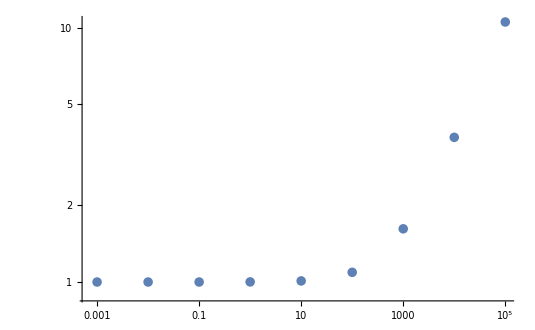

```mathematica
ListLogLogPlot[data]
```

```mathematica
z = DSolve[y'[t] == 100 - 0.2*y[t] - 1000*y[t]*(y[t]-1), y[t],t];
Natom = Limit[y[t],t->Infinity]/.z
```

{1.09142}

```mathematica
Nequil[[6]]
```

{1.09142}

```mathematica
Nequil
```

{{0.999801},{0.99981},{0.9999},{1.0008},{1.0097},{1.09142}}

```mathematica
LoadR
```

{1/1000,1/100,1/10,1,10,100}

```mathematica
Natom
```

{10.5124}

```mathematica
Information[Natom]
```

Global`Natom

Natom={10.5124}

```mathematica
N[Natom]
```

{10.5124}

```mathematica
Natom[[1]]
```

10.5124